```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F12"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F12\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,30]
,15,0.000001],1500<#[[1]]<6000&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.816},{loc[[-1,1]],0}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,10],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],30],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],30]
,15,0.000001],1500<#[[1]]<6000&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,22},1,Length[data2],1}]
```

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],PlotRange->{{-0.010,0.02},{0.8,1}},Joined->True,Epilog->Line[{{-2,1},{2,1}}]],{{i,2},1,Length[data2],1}]
```

```mathematica
power[[46]]
```

15

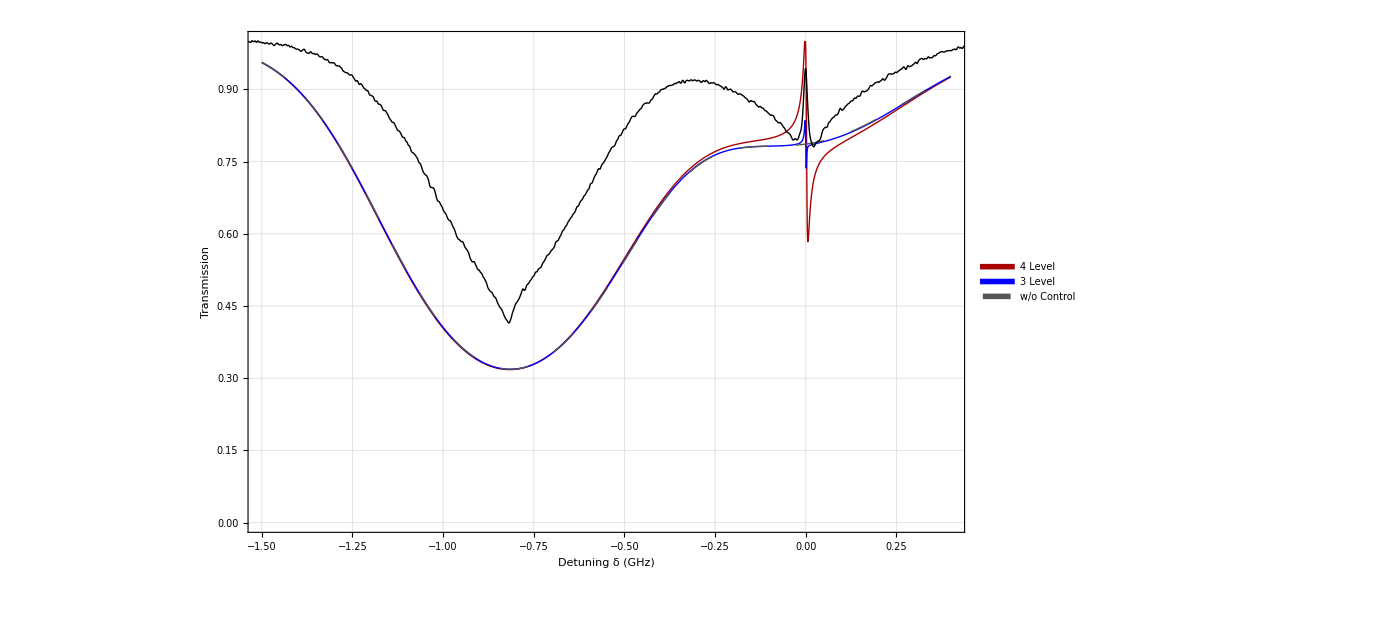

```mathematica
final2=ListPlot[{Lev4DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,0*10^6,0],Lev3DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,0*10^6,0],Lev3DoppTestsc[32,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[1],Darker[Red]},{AbsoluteThickness[1],Blue},{AbsoluteThickness[1],Darker[Gray],Dashing[.02]},{AbsoluteThickness[1],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-1.5,0.4},{0.0,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[45]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmax8712=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],0<#[[1]]<0.01&][[All,2]]//Max,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01<#[[1]]<0.02&][[All,2]]//Max],{i,1,Length[data],1}];
EITmin8712=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],0<#[[1]]<0.01&][[All,2]]//Min,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01<#[[1]]<0.02&][[All,2]]//Min],{i,1,Length[data],1}];
```

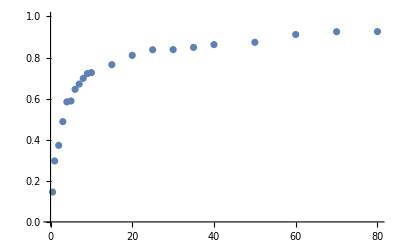

```mathematica
rb8712=ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax8712,4]]/Log[Min/@Partition[EITmin8712,4]]}]},PlotRange->{0,1}]
```

```mathematica
Table[Select[Transpose[f[data2off[[1]]][[{4,2}]]],-0.02<#[[1]]<0.02&][[All,2]]//Min,{i,1,Length[dataoff],1}]//Mean
```

0.808096